```mathematica
xp =NDSolveValue[{x''[t]+δ x'[t]+α x[t]+βx[t]^3==γ Cos[ω t],x[0]==0,x'[0]==0.12} /. {δ->0.15,α->-1,β->1,γ->0.3,ω->1},x,{t,0,100}]
```

InterpolatingFunction[…]

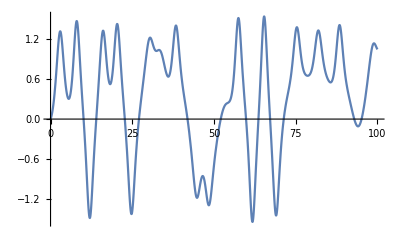

```mathematica
Plot[xp[t],{t,0,100}]
```

```mathematica
output=Table[xp[t],{t,0.01,10,0.005}];
input=Table[t,{t,0.01,10,0.005}];
```

```mathematica
data0=RandomSample[Thread[input->output]];
```

```mathematica
Take[data0,10]
```

{6.6→0.597219,3.22→1.2732,3.98→0.859878,8.94→0.919132,7.295→1.11056,0.74→0.171019,7.575→1.31685,4.185→0.734692,5.725→0.309545,3.05→1.30891}

```mathematica
s=Dimensions[data0][[1]];
data=Table[data0[[i,1]]->{data0[[i,2]]},{i,1,s-1,1}];
training=RandomSample[data[[1;;Ceiling[0.8s]]]];
validation=RandomSample[data[[Ceiling[0.8s]+1;;]]];
```

```mathematica
net=NetChain[{32,Tanh,16,Tanh,1}];
net2=NetChain[{32,Tanh,16,Tanh,1}](*32,Tanh,4,Tanh,1 is pretty good*)
```

NetChain[<>]

```mathematica
trainedData=NetTrain[net2,training]
```

NetChain[<>]

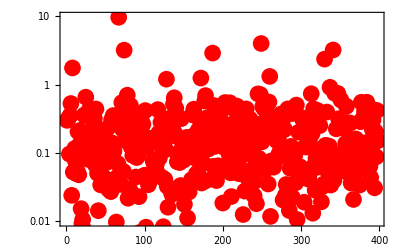

```mathematica
ListLogPlot[
Flatten[
Abs[(trainedData/@validation[[All,1]]-validation[[All,2]])*100/validation[[All,2]]]
],PlotRange->{All,{0,10}},Frame->True,FrameStyle->Black,PlotStyle->{Red, PointSize->0.03}]
```